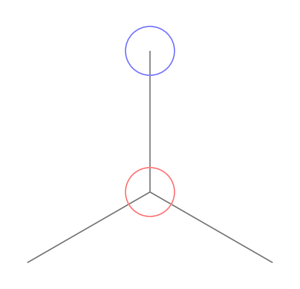

```mathematica
Clear["Global`*"]
unitCell[x_,y_]:={Gray,
,Line[{{x,y},{x,y+1/Sqrt[3]}}],Line[{{x,y},{x+1/2,y-1/(2*Sqrt[3])}}],Line[{{x,y},{x-1/2,y-1/(2*Sqrt[3])}}],Lighter[Red,0.5],Circle[{x,y},0.1],Lighter[Blue,0.5],Circle[{x,y+1/Sqrt[3]},0.1]};
Graphics[unitCell[0,0],ImageSize->300]
```

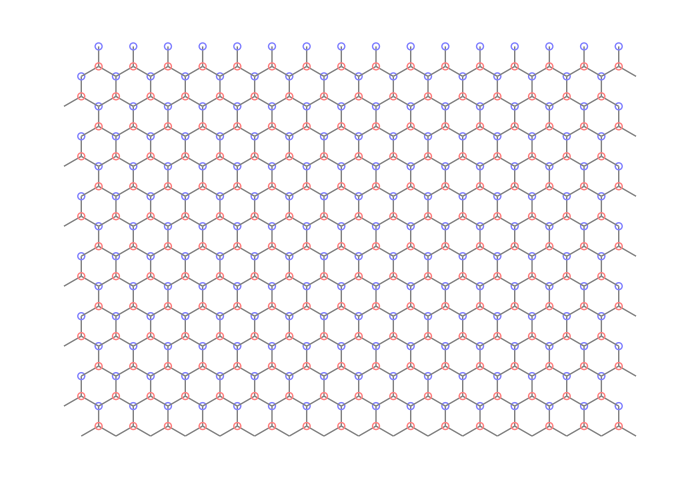

```mathematica
Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,1,13},{k,Ceiling[j/2],15+Ceiling[j/2]}]],ImageSize->700]
```